```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.450033},{0.01,-0.446444},{0.02,-0.442969},{0.03,-0.439596},{0.04,-0.436322},{0.05,-0.433142},{0.06,-0.430055},{0.07,-0.427056},{0.08,-0.42414},{0.09,-0.421304},{0.1,-0.418542},{0.11,-0.415857},{0.12,-0.413234},{0.13,-0.410683},{0.14,-0.408186},{0.15,-0.405754},{0.16,-0.403368},{0.17,-0.40104},{0.18,-0.398754},{0.19,-0.396513},{0.2,-0.394314},{0.21,-0.392145},{0.22,-0.390017},{0.23,-0.387906},{0.24,-0.385832},{0.25,-0.383787},{0.26,-0.381745},{0.27,-0.379717},{0.28,-0.377719},{0.29,-0.375725},{0.3,-0.373716},{0.31,-0.371725},{0.32,-0.369742},{0.33,-0.367742},{0.34,-0.365717},{0.35,-0.3637},{0.36,-0.361673},{0.37,-0.359615},{0.38,-0.357519},{0.39,-0.355414},{0.4,-0.353285},{0.41,-0.351115},{0.42,-0.348895},{0.43,-0.346641},{0.44,-0.344341},{0.45,-0.341991},{0.46,-0.339588},{0.47,-0.337128},{0.48,-0.334606},{0.49,-0.332019},{0.5,-0.329361},{0.51,-0.326631},{0.52,-0.323821},{0.53,-0.320932},{0.54,-0.317955},{0.55,-0.314888},{0.56,-0.311727},{0.57,-0.308466},{0.58,-0.305102},{0.59,-0.301629},{0.6,-0.298045},{0.61,-0.294344},{0.62,-0.290521},{0.63,-0.286571},{0.64,-0.282491},{0.65,-0.278275},{0.66,-0.273918},{0.67,-0.269417},{0.68,-0.264765},{0.69,-0.259958},{0.7,-0.254991},{0.71,-0.249857},{0.72,-0.244555},{0.73,-0.239076},{0.74,-0.233417},{0.75,-0.227572},{0.76,-0.221535},{0.77,-0.215302},{0.78,-0.208867},{0.79,-0.202224},{0.8,-0.195366},{0.81,-0.188292},{0.82,-0.180993},{0.83,-0.173461},{0.84,-0.165697},{0.85,-0.157687},{0.86,-0.149432},{0.87,-0.140922},{0.88,-0.13215},{0.89,-0.123116},{0.9,-0.113803},{0.91,-0.104217},{0.92,-0.0943382},{0.93,-0.0841736},{0.94,-0.0737025},{0.95,-0.0629307},{0.96,-0.0518393},{0.97,-0.0404302},{0.98,-0.0286884},{0.99,-0.01661},{1.,-0.00418454}}

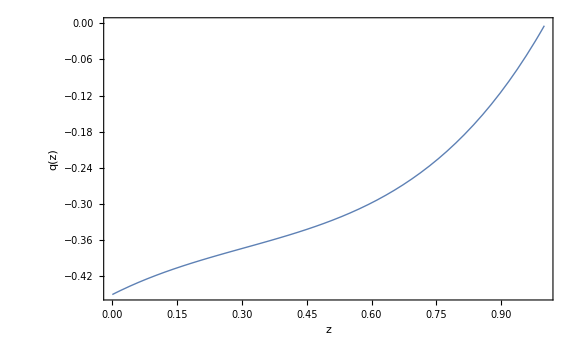

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.690827},{0.01,-0.675469},{0.02,-0.660393},{0.03,-0.645588},{0.04,-0.63105},{0.05,-0.616771},{0.06,-0.602746},{0.07,-0.588968},{0.08,-0.57543},{0.09,-0.562127},{0.1,-0.549052},{0.11,-0.536201},{0.12,-0.523566},{0.13,-0.511144},{0.14,-0.498926},{0.15,-0.486913},{0.16,-0.475092},{0.17,-0.463464},{0.18,-0.452024},{0.19,-0.440762},{0.2,-0.429681},{0.21,-0.418771},{0.22,-0.408027},{0.23,-0.39745},{0.24,-0.387033},{0.25,-0.376768},{0.26,-0.36666},{0.27,-0.356699},{0.28,-0.346878},{0.29,-0.337204},{0.3,-0.327667},{0.31,-0.318259},{0.32,-0.308985},{0.33,-0.299842},{0.34,-0.290824},{0.35,-0.281921},{0.36,-0.273137},{0.37,-0.264476},{0.38,-0.255928},{0.39,-0.247487},{0.4,-0.239148},{0.41,-0.230921},{0.42,-0.222801},{0.43,-0.21478},{0.44,-0.206853},{0.45,-0.199017},{0.46,-0.191283},{0.47,-0.183643},{0.48,-0.176092},{0.49,-0.168625},{0.5,-0.161238},{0.51,-0.153942},{0.52,-0.146731},{0.53,-0.139601},{0.54,-0.132546},{0.55,-0.125564},{0.56,-0.118657},{0.57,-0.111829},{0.58,-0.105076},{0.59,-0.0983938},{0.6,-0.0917777},{0.61,-0.0852249},{0.62,-0.0787396},{0.63,-0.0723242},{0.64,-0.065975},{0.65,-0.0596888},{0.66,-0.0534623},{0.67,-0.0472929},{0.68,-0.0411833},{0.69,-0.0351337},{0.7,-0.0291416},{0.71,-0.0232052},{0.72,-0.0173245},{0.73,-0.0114977},{0.74,-0.00572448},{0.75,-3.35809×10^-6},{0.76,0.00566607},{0.77,0.0112849},{0.78,0.016854},{0.79,0.0223739},{0.8,0.0278461},{0.81,0.0332704},{0.82,0.0386477},{0.83,0.0439795},{0.84,0.049266},{0.85,0.0545075},{0.86,0.059705},{0.87,0.0648594},{0.88,0.0699709},{0.89,0.0750402},{0.9,0.0800681},{0.91,0.0850549},{0.92,0.0900012},{0.93,0.0949075},{0.94,0.0997745},{0.95,0.104602},{0.96,0.109392},{0.97,0.114143},{0.98,0.118857},{0.99,0.123534},{1.,0.128174}}

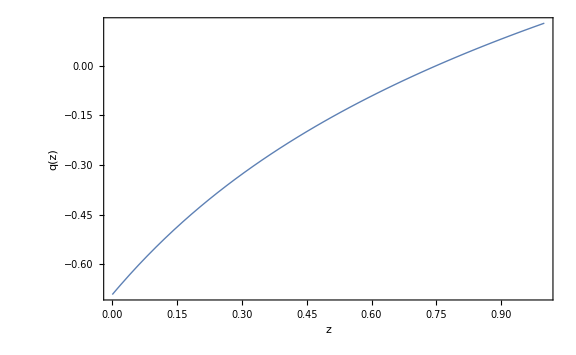

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.17242},{0.01,-1.12256},{0.02,-1.0745},{0.03,-1.02817},{0.04,-0.983509},{0.05,-0.940457},{0.06,-0.898955},{0.07,-0.858946},{0.08,-0.820366},{0.09,-0.783174},{0.1,-0.747302},{0.11,-0.712715},{0.12,-0.679348},{0.13,-0.647166},{0.14,-0.616112},{0.15,-0.586152},{0.16,-0.557235},{0.17,-0.529323},{0.18,-0.502379},{0.19,-0.476359},{0.2,-0.451239},{0.21,-0.426967},{0.22,-0.403511},{0.23,-0.380848},{0.24,-0.358957},{0.25,-0.337788},{0.26,-0.317314},{0.27,-0.297517},{0.28,-0.278374},{0.29,-0.259846},{0.3,-0.241914},{0.31,-0.224561},{0.32,-0.207767},{0.33,-0.191498},{0.34,-0.175738},{0.35,-0.160473},{0.36,-0.14569},{0.37,-0.131356},{0.38,-0.117457},{0.39,-0.103983},{0.4,-0.0909221},{0.41,-0.0782528},{0.42,-0.0659548},{0.43,-0.0540196},{0.44,-0.0424381},{0.45,-0.031201},{0.46,-0.0202856},{0.47,-0.00967957},{0.48,0.000623975},{0.49,0.0106319},{0.5,0.0203517},{0.51,0.0298027},{0.52,0.0389962},{0.53,0.0479373},{0.54,0.0566312},{0.55,0.0650835},{0.56,0.073305},{0.57,0.0813123},{0.58,0.0891093},{0.59,0.0967},{0.6,0.104088},{0.61,0.111278},{0.62,0.118284},{0.63,0.125114},{0.64,0.13177},{0.65,0.138256},{0.66,0.144575},{0.67,0.150735},{0.68,0.156746},{0.69,0.16261},{0.7,0.168331},{0.71,0.173908},{0.72,0.179347},{0.73,0.184659},{0.74,0.189848},{0.75,0.194915},{0.76,0.199861},{0.77,0.204687},{0.78,0.209399},{0.79,0.214006},{0.8,0.218511},{0.81,0.222914},{0.82,0.227216},{0.83,0.231419},{0.84,0.235524},{0.85,0.239542},{0.86,0.243475},{0.87,0.247321},{0.88,0.251083},{0.89,0.25476},{0.9,0.258359},{0.91,0.261884},{0.92,0.265335},{0.93,0.268714},{0.94,0.272019},{0.95,0.275253},{0.96,0.278424},{0.97,0.281532},{0.98,0.284576},{0.99,0.287558},{1.,0.290477}}

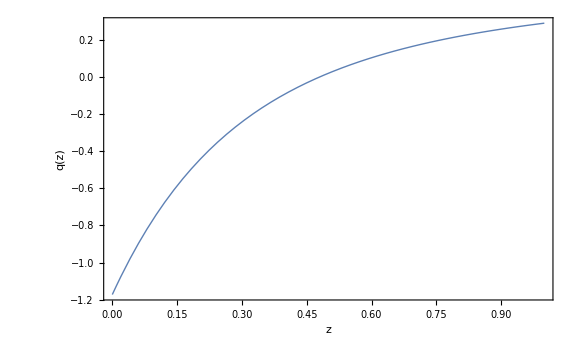

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.41321},{0.01,-1.34076},{0.02,-1.27167},{0.03,-1.20579},{0.04,-1.14295},{0.05,-1.08302},{0.06,-1.02583},{0.07,-0.971256},{0.08,-0.919175},{0.09,-0.869452},{0.1,-0.821964},{0.11,-0.776608},{0.12,-0.733273},{0.13,-0.691851},{0.14,-0.652256},{0.15,-0.614379},{0.16,-0.578159},{0.17,-0.543482},{0.18,-0.510298},{0.19,-0.478513},{0.2,-0.448064},{0.21,-0.418893},{0.22,-0.390919},{0.23,-0.364102},{0.24,-0.338372},{0.25,-0.313677},{0.26,-0.289979},{0.27,-0.267213},{0.28,-0.245343},{0.29,-0.224333},{0.3,-0.204126},{0.31,-0.184696},{0.32,-0.166026},{0.33,-0.148038},{0.34,-0.130706},{0.35,-0.114012},{0.36,-0.0979365},{0.37,-0.0824601},{0.38,-0.0675544},{0.39,-0.0531625},{0.4,-0.0392697},{0.41,-0.0258629},{0.42,-0.0129285},{0.43,-0.000451379},{0.44,0.0116093},{0.45,0.0232724},{0.46,0.0345472},{0.47,0.0454434},{0.48,0.0559706},{0.49,0.0661567},{0.5,0.0760228},{0.51,0.085575},{0.52,0.09482},{0.53,0.103767},{0.54,0.112443},{0.55,0.120855},{0.56,0.129009},{0.57,0.13691},{0.58,0.144569},{0.59,0.152008},{0.6,0.159231},{0.61,0.166241},{0.62,0.173042},{0.63,0.179642},{0.64,0.186062},{0.65,0.192305},{0.66,0.198373},{0.67,0.204267},{0.68,0.209992},{0.69,0.215567},{0.7,0.220996},{0.71,0.226278},{0.72,0.231415},{0.73,0.236413},{0.74,0.241286},{0.75,0.246036},{0.76,0.250662},{0.77,0.255165},{0.78,0.259551},{0.79,0.263834},{0.8,0.268013},{0.81,0.272088},{0.82,0.276059},{0.83,0.279928},{0.84,0.28371},{0.85,0.287405},{0.86,0.291014},{0.87,0.294535},{0.88,0.297969},{0.89,0.301322},{0.9,0.304605},{0.91,0.307816},{0.92,0.310954},{0.93,0.314018},{0.94,0.317009},{0.95,0.319937},{0.96,0.322805},{0.97,0.325612},{0.98,0.328357},{0.99,0.331038},{1.,0.333667}}

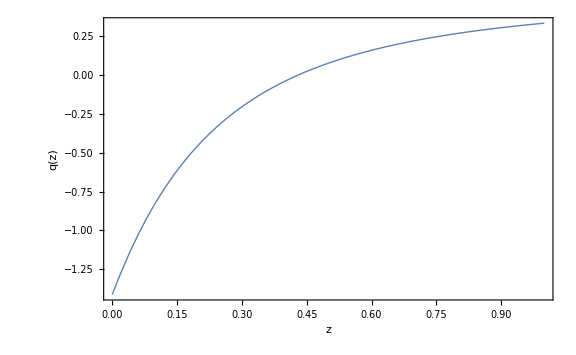

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

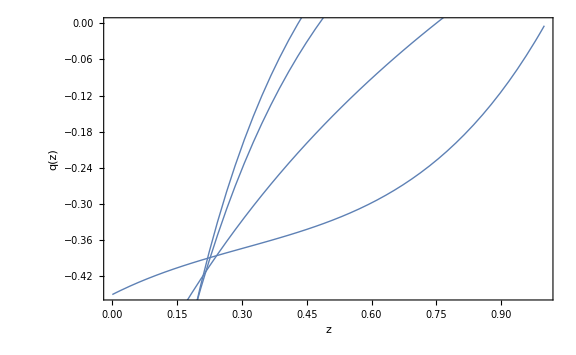

```mathematica
Show[p04n, p02n, p02, p04]
```

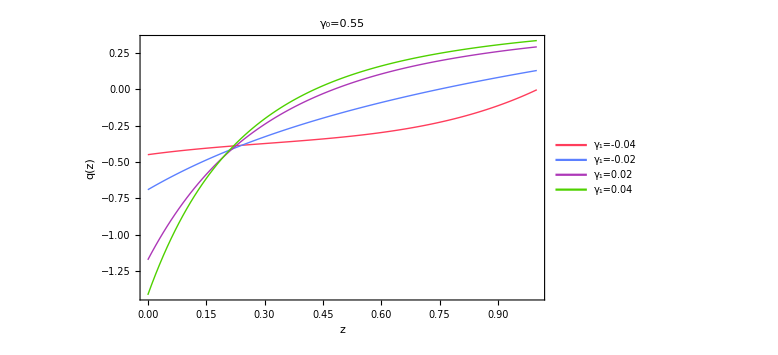

```mathematica
list2=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}, {Thick, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["q(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
SetDirectory["C:\\Users\\Gerald\\Desktop\\7sem\\dark energy\\plots_paper"]
```

C:\Users\Gerald\Desktop\7sem\dark energy\plots_paper

```mathematica
Export["q(z)_gamma055.pdf",list2,ImageResolution->500]
```

q(z)_gamma055.pdf